# MAD-X TFS file reader

## Function Definitions

```mathematica
madFile[file_]:=Module[
{d,h,dPos,cols},
d=Import[file,"Table"];
h=Cases[d,{"@",___}|{"*",___}|{"$",___}];
d=Cases[d,Except[{"@",___}|{"*",___}|{"$",___}]];
cols=Rest@First@Cases[h,{"*",___}];
d=Thread[Rule@@{cols,Transpose@d}];
{h,d} (*extracts headings and data from a mad file*)
];
madFileToDataset::usage="Takes a mad optics file and returns {header, data}, where data is a Dataset with the columns specified as in the mad file.";
madFileToDataset[file_]:=Module[
{header,data,assocs,keys},
{header,data}=madFile[file];
keys=Keys[data];
assocs=Association[Thread[Rule[keys,#]]]&/@Transpose[keys/.data];
{header,Dataset[assocs]}
];

getTwissAtElement::usage="Takes a string and a data set and returns the list {\"BETX\",\"ALFX\",\"MUX\",\"BETY\",\"ALFY\",\"MUY\"} for the specified element.";
getTwissAtElement[element_String,opticsSet_Dataset]:=Module[
{entry,twiss},
entry=opticsSet[Select[StringMatchQ[element,#NAME]&]];
entry=First[Normal[entry]];
twiss=entry[[Key[#]]]&/@{"BETX","ALFX","MUX","BETY","ALFY","MUY"};
twiss
];

getSAtElement::usage="Takes a string and a data set and returns the s value for the specified element.";
getSAtElement[element_String,opticsSet_Dataset]:=Module[
{entry,s},
entry=opticsSet[Select[StringMatchQ[element,#NAME]&]];
entry=First[Normal[entry]];
s=entry[[Key["S"]]];
s
];

variancesSub:: usage="finds the variance of a single-variable weighted data list from a file";
variancesSub[file_]:=Module[
{x,w,tabX},
tabX=Import[file,"Table"];
{x,w}=Drop[Transpose[tabX],1];
Variance @ WeightedData[x,w]
]

variances:: usage="calculates x, y, and xy variances from input data lists and outputs them in a list of three";
variances[num_Integer,xData_List,yData_List,dData_List]:=Module[ 
{numb,sigx,sigy,sigd,vars},
numb=num;
sigx=variancesSub@xData[[numb]];
sigy=variancesSub@yData[[numb]];
sigd=variancesSub@dData[[numb]];
sigd=sigd-0.5*(sigx+sigy);
vars={sigx,sigy,sigd}
];

covar4x4Calc::usage="fills a 4x4 covariance matrix with data from an 6xN data table";
covar4x4Calc[tab_]:=Module[
{correlationData, numLines, averages, empty},
correlationData=Drop[Transpose[tab],-2];
numLines=Length@correlationData[[1]];
averages={Mean[correlationData[[1]]],Mean[correlationData[[2]]],Mean[correlationData[[3]]],Mean[correlationData[[4]]]};
(*order: x, xp, y, yp*)
empty={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
Module[{i,j,k},
For[j=1,j≤4,j++,
For[k=1,k≤4,k++,
empty[[k,j]]=(1/numLines)*∑_(i=1)^numLines ((correlationData[[k,i]]-averages[[k]])(correlationData[[j,i]]-averages[[j]]));
];];];
empty
];

covarToCorr::usage="constructs a 4x4 correlation matrix from a 4x4 covariance matrix, with 1 all along the diagonal";
covarToCorr[mat_]:=Module[
{sigX,sigXP,sigY,sigYP, sigList,mat2},
sigX=(mat[[1,1]])^(1/2);
sigXP=(mat[[2,2]])^(1/2);
sigY=(mat[[3,3]])^(1/2);
sigYP=(mat[[4,4]])^(1/2);
sigList={sigX,sigXP,sigY,sigYP};
mat2=Table[
mat[[m,n]]/(sigList[[m]]*sigList[[n]])
,{m,1,4}
,{n,1,4}
];
mat2 
];
```

## Definitions

```mathematica
(* 10x, 10y, s=.01 *)


startPos="SURV$START"; (****INPUT NEEDED****) (*reconstruction point, s0, string*)
endPos ={"WS02","WS20","WS21","WS23","WS24"}; (****INPUT NEEDED****) (* which wire scanners to use *)(*wire scanner location LIST of strings*)
fileLists={                           (* specify folder(s) *)
Flatten[FileNames[FileNameJoin[{"/Users/4tc/Dropbox/suli 2018 project/*_optics_*","BeamInfo.mu.txt"}]]]};
fileLists=fileLists[[1]]

somwsFile=fileLists[[1]] ;(*contains BET, ALF, MU data*) (****INPUT NEEDED****) (* which optics to use *)
{somwsDataHeader,somwsDataSet}=madFileToDataset[somwsFile];

moswsEndPos =endPos[[2]]; (****INPUT NEEDED****) (*ONE wire scanner location, string*)

comboList=Transpose[madFileToDataset[#]&/@fileLists];
{comboDataHeaders,comboDataSets}=comboList;
```

{/Users/4tc/Dropbox/suli 2018 project/x_optics_0001/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0002/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0003/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0004/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0005/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0006/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0007/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0008/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0009/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/x_optics_0010/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0001/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0002/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0003/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0004/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0005/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0006/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0007/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0008/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0009/BeamInfo.mu.txt,/Users/4tc/Dropbox/suli 2018 project/y_optics_0010/BeamInfo.mu.txt}

## Twiss Parameters Example

```mathematica
fileLists={
FileNameJoin[{NotebookDirectory[],"optics-test-1"}],
FileNameJoin[{NotebookDirectory[],"optics-test-2"}]
};

{header,dataSet}=madFileToDataset[fileLists[[1]]];
dataSet (*Comment/uncomment to hide/view the data set.*)
getTwissAtElement["QTV_C11",dataSet]

(*Applying to a list of fileLists.*)

{#,getTwissAtElement["QTV_C11",Last@madFileToDataset[#]]}&/@fileLists;
```

Dataset[<>]

{14.5012,0.573589,0.177203,15.5281,0.505342,0.142294}

```mathematica
TwissPos1=getTwissAtElement["Q25",dataSet] (*first location*)
TwissPos2=getTwissAtElement["MARK",dataSet] (*second location*)
```

{6.2227,-0.630381,2.83076,17.0843,1.66486,3.01741}

{68.9826,1.07345,3.39659,7.05838,-0.183575,3.40026}

## R Transform Matrix (RTM) Definition

```mathematica
ClearAll[rTransformMatrix];
rTransformMatrix[{βx1_,αx1_,μx1uncor_,βy1_,αy1_,μy1uncor_},{βx2_,αx2_,μx2uncor_,βy2_,αy2_,μy2uncor_}]:=Module[{μx2=μx2uncor*2*π,μx1=μx1uncor*2*π,μy2=μy2uncor*2*π,μy1=μy1uncor*2*π},{{√(βx2/βx1)(Cos[μx2-μx1]+αx1*Sin[μx2-μx1]),√(βx2*βx1)Sin[μx2-μx1],0,0},
{(-(1+αx2*αx1))/(√(βx2*βx1))Sin[μx2-μx1]+(αx1-αx2)/(√(βx2*βx1))Cos[μx2-μx1],√(βx1/βx2)(Cos[μx2-μx1]-αx2*Sin[μx2-μx1]),0,0},
{0,0,√(βy2/βy1)(Cos[μy2-μy1]+αy1*Sin[μy2-μy1]),√(βy2*βy1)Sin[μy2-μy1]},
{0,0,(-(1+αy2*αy1))/(√(βy2*βy1))Sin[μy2-μy1]+(αy1-αy2)/(√(βy2*βy1))Cos[μy2-μy1],√(βy1/βy2)(Cos[μy2-μy1]-αy2*Sin[μy2-μy1])}}]
```

Test R Matrix

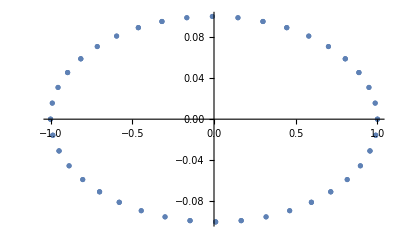
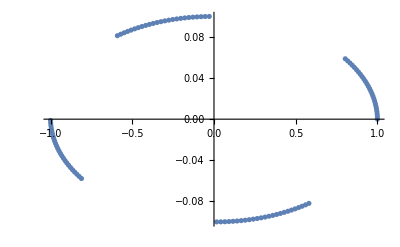

```mathematica
Module[
{test,tracked},
test=rTransformMatrix[{10,0.01,0,10,0.01,0},{10,0.01,0.225,10,0.01,0.249}];
tracked=NestList[test.#&,{1,0,1,0},100];
{ListPlot[tracked[[;;,{1,2}]]],ListPlot[tracked[[;;,{3,4}]]]}
]
```

## Calculate R - Single Optics, Multiple WS (SOMWS)

```mathematica
somwsStartTwiss=getTwissAtElement[startPos,somwsDataSet]; (*get twiss at start*)
somwsEndTwiss1=getTwissAtElement[endPos[[1]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss2=getTwissAtElement[endPos[[2]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss3=getTwissAtElement[endPos[[3]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss4=getTwissAtElement[endPos[[4]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss5=getTwissAtElement[endPos[[5]],somwsDataSet]; (*get twiss at one endpoint*)

somwsR1=rTransformMatrix[somwsStartTwiss,somwsEndTwiss1];(*calculate RTM*)
somwsR2=rTransformMatrix[somwsStartTwiss,somwsEndTwiss2];(*calculate RTM*)
somwsR3=rTransformMatrix[somwsStartTwiss,somwsEndTwiss3];(*calculate RTM*)
somwsR4=rTransformMatrix[somwsStartTwiss,somwsEndTwiss4]; (*calculate RTM*)
somwsR5=rTransformMatrix[somwsStartTwiss,somwsEndTwiss5]; (*calculate RTM*)
somwsRs={somwsR1, somwsR2,somwsR3, somwsR4,somwsR5};
MatrixForm/@somwsRs
```

{(-0.632229 | 3.80004 | 0 | 0
-0.385097 | 0.732941 | 0 | 0
0 | 0 | 2.78656 | 6.10843
0 | 0 | 0.423158 | 1.28647),(-3.22624 | 8.92993 | 0 | 0
1.39983 | -4.18456 | 0 | 0
0 | 0 | -5.4254 | -13.4608
0 | 0 | -0.534347 | -1.51007),(2.0025 | -7.33236 | 0 | 0
0.981937 | -3.09609 | 0 | 0
0 | 0 | -2.97424 | -8.13112
0 | 0 | 0.756353 | 1.73154),(10.4298 | -31.3023 | 0 | 0
1.21024 | -3.53633 | 0 | 0
0 | 0 | 1.88726 | 2.99383
0 | 0 | 0.237387 | 0.906447),(5.50935 | -16.089 | 0 | 0
-1.33068 | 4.06751 | 0 | 0
0 | 0 | 5.48555 | 12.3175
0 | 0 | 0.71856 | 1.79578)}

## Calculate R - Multiple Optics, Single WS (MOSWS)

```mathematica
(*apply to full list of fileLists*)
moswsStartTwiss=getTwissAtElement[startPos,Last@madFileToDataset[#]]&/@fileLists;(*get twiss at start, list of 6-item lists*)
moswsEndTwiss=getTwissAtElement[moswsEndPos,Last@madFileToDataset[#]]&/@fileLists; (*get twiss at end, list of 6-item lists*)

moswsRs=Table[
rTransformMatrix[moswsStartTwiss[[j]],moswsEndTwiss[[j]]],(*calculate RTM*)
{j,1,Length@moswsEndTwiss}
];
ClearAll[j];
MatrixForm/@moswsRs
```

{(-3.22624 | 8.92993 | 0 | 0
1.39983 | -4.18456 | 0 | 0
0 | 0 | -5.4254 | -13.4608
0 | 0 | -0.534347 | -1.51007),(-3.10121 | 8.50111 | 0 | 0
1.34145 | -3.99967 | 0 | 0
0 | 0 | 6.75243 | 19.0668
0 | 0 | 0.599258 | 1.84022),(-3.02509 | 8.207 | 0 | 0
1.40131 | -4.13229 | 0 | 0
0 | 0 | -3.60717 | -10.0144
0 | 0 | -0.381691 | -1.3369),(-2.93839 | 7.88308 | 0 | 0
1.4344 | -4.18851 | 0 | 0
0 | 0 | -3.46715 | -7.58331
0 | 0 | -0.557655 | -1.50812),(-2.8207 | 7.4753 | 0 | 0
1.43628 | -4.16088 | 0 | 0
0 | 0 | 2.33717 | 1.73431
0 | 0 | 0.426914 | 0.744661),(-2.29424 | 5.99831 | 0 | 0
1.11573 | -3.35295 | 0 | 0
0 | 0 | -3.64821 | -14.4421
0 | 0 | -0.193317 | -1.03939),(-1.97465 | 5.08488 | 0 | 0
0.648754 | -2.17701 | 0 | 0
0 | 0 | -2.76278 | -10.2108
0 | 0 | -0.0436857 | -0.523411),(-1.85971 | 4.70661 | 0 | 0
1.42403 | -4.1417 | 0 | 0
0 | 0 | -2.26887 | -10.3421
0 | 0 | -0.0499438 | -0.668404),(-1.87274 | 4.64521 | 0 | 0
1.34679 | -3.8746 | 0 | 0
0 | 0 | -3.36704 | -9.21531
0 | 0 | -0.367434 | -1.30263),(-0.131413 | -0.729485 | 0 | 0
0.917834 | -2.51462 | 0 | 0
0 | 0 | 0.837457 | 7.84999
0 | 0 | -0.093575 | 0.316956),(2.5478 | -8.0533 | 0 | 0
-0.309387 | 1.37043 | 0 | 0
0 | 0 | -2.23404 | -4.70864
0 | 0 | -0.495602 | -1.49219),(2.33618 | -7.49498 | 0 | 0
-0.044878 | 0.572028 | 0 | 0
0 | 0 | -5.28885 | -11.6817
0 | 0 | -0.688398 | -1.70957),(1.62605 | -5.66794 | 0 | 0
0.473509 | -1.03553 | 0 | 0
0 | 0 | -2.54873 | -5.8539
0 | 0 | -0.446443 | -1.41774),(2.44058 | -7.58194 | 0 | 0
0.0902364 | 0.129409 | 0 | 0
0 | 0 | -2.7558 | -6.54429
0 | 0 | -0.389413 | -1.28763),(2.62018 | -8.23898 | 0 | 0
-0.0380116 | 0.501178 | 0 | 0
0 | 0 | -2.8997 | -7.08911
0 | 0 | -0.507615 | -1.58587),(2.3868 | -7.41173 | 0 | 0
0.519368 | -1.19383 | 0 | 0
0 | 0 | -3.7564 | -9.42296
0 | 0 | -0.445056 | -1.38264),(-1.96663 | 4.75659 | 0 | 0
1.20555 | -3.42428 | 0 | 0
0 | 0 | -4.81947 | -12.3726
0 | 0 | -0.613025 | -1.78126),(2.15724 | -6.83479 | 0 | 0
0.673538 | -1.67042 | 0 | 0
0 | 0 | -5.6391 | -14.7851
0 | 0 | -0.628922 | -1.82629),(2.46373 | -7.52086 | 0 | 0
0.444823 | -0.951994 | 0 | 0
0 | 0 | -3.71629 | -9.93469
0 | 0 | -0.427299 | -1.41137),(2.39208 | -7.44963 | 0 | 0
0.472804 | -1.0544 | 0 | 0
0 | 0 | -3.40266 | -9.26232
0 | 0 | -0.400176 | -1.3832)}

## Calculate R - Combination SOMWS and MOSWS (COMBO)

```mathematica
(*apply to full list of fileLists*)
comboStartTwiss=getTwissAtElement[startPos,#]&/@comboDataSets; (*get twiss at start, N-item list of 6-item lists*)
(*comboEndTwiss={getTwissAtElement[endPos[[1]],#]&/@comboDataSets,
getTwissAtElement[endPos[[2]],#]&/@comboDataSets,
getTwissAtElement[endPos[[3]],#]&/@comboDataSets,
getTwissAtElement[endPos[[4]],#]&/@comboDataSets,
getTwissAtElement[endPos[[5]],#]&/@comboDataSets};(*get twiss at end. 5-item list of N-item lists of 6-item lists*) 

comboEndTwiss2=Transpose[comboEndTwiss,{2,1,3}] (*sort by optics, then position, then twiss*)*)

comboEndTwiss=Table[   (* sorted by optics, then position, then twiss *)
getTwissAtElement[endPos[[i]],comboDataSets[[j]]],
{j,1,Length@comboDataSets},
{i,1,5}
];(* N-item list of 5-item lists of 6-item lists *)

comboRs=Table[
rTransformMatrix[comboStartTwiss[[j]],comboEndTwiss[[j,k]] ],(*calculate RTM*)
{k,1,Length@endPos}, (* for all wire scanners *)
{j,1,Length@comboEndTwiss} (* for all optics *)
];
ClearAll[j,k];

comboRs=Flatten[comboRs,1]; 
MatrixForm/@comboRs;
Length@comboRs;
```

## Build Measurement Matrix

```mathematica
(****INPUT NEEDED****)(*what measurements?*)

(*moswsRs={};*) (*<-- uncomment to test with empty set*)
(*listOfRs=somwsRs;*)
(*listOfRs=moswsRs;*)
(*listOfRs=Join[somwsRs, moswsRs];*)
listOfRs=comboRs;

ClearAll[r,σ,orderedSigmaElements,generalMeasurementMatrix]
{orderedSigmaElements,generalMeasurementMatrix}=Module[
{
rmat=Table[r[i,j],{i,1,4},{j,1,4}],
σmat=Table[σ[Min[i,j],Max[i,j]],{i,1,4},{j,1,4}],
unknowns,
trans,coefficients,dummy=Array[0&,{10,3}]
},
trans=(rmat.σmat.Transpose[rmat])[[Sequence@@#]]&/@{{1,1},{3,3},{1,3}};(*Take elements xx,yy,xy from σ'*)
unknowns=DeleteDuplicates[Flatten[σmat]];(*This is how our unknown column vector will be ordered, so we'll save it at the end.*)
coefficients=Table[{#,Coefficient[trans[[i]],#,1]}&/@unknowns,{i,1,Length@trans}];(*We extract the coeffecients in terms of r for each element of σ, each unknown.*)
{unknowns,Table[coefficients[[i,j,2]],{i,1,Length@trans},{j,1,Length@unknowns}]}
];

(*We can set the coupling elements to 0.*)
uncoupledMeasurementMatrix=generalMeasurementMatrix/.{r[1,3]->0,r[1,4]->0,r[2,3]->0,r[2,4]->0,r[3,1]->0,r[3,2]->0,r[4,2]->0,r[4,1]->0};

(*
Using the notation r[scanIndex][plane index,σ index] we can give the full uncoupled measurement matrix in general form. From here solving the problem is just a matter of taking the least squares where the answer will be returned as {...10 numbers...}. 
*)

fullUncoupledMeasurementMatrix=Join@@Table[
uncoupledMeasurementMatrix/.Flatten[Table[r[i,j]->r[scanIndex][i,j],{i,1,4},{j,1,4}]],
{scanIndex,1,Length@listOfRs}
];
MatrixForm@fullUncoupledMeasurementMatrix;
For[ (* define all r terms in meas matrix *)
i=1,i≤Length@listOfRs,i++,
rules={r[i][1,1]->listOfRs[[i]][[1,1]],r[i][1,2]->listOfRs[[i]][[1,2]],
r[i][2,1]->listOfRs[[i]][[2,1]],r[i][2,2]->listOfRs[[i]][[2,2]],
r[i][3,3]->listOfRs[[i]][[3,3]],r[i][3,4]->listOfRs[[i]][[3,4]],
r[i][4,3]->listOfRs[[i]][[4,3]],r[i][4,4]->listOfRs[[i]][[4,4]]};
fullUncoupledMeasurementMatrix=fullUncoupledMeasurementMatrix/.rules;
];
ClearAll[i];

MatrixForm@fullUncoupledMeasurementMatrix;
```

## Sigma Matrix Reconstruction

Wire Scanner Measurements

```mathematica
dataWSX=FileNames[{"~/Dropbox/suli 2018 project/*_optics*/ws_*_x.dat"}] ;(* specify folder(s) *)
dataWSY=FileNames[{"~/Dropbox/suli 2018 project/*_optics*/ws_*_y.dat"}];
dataWSD=FileNames[{"~/Dropbox/suli 2018 project/*_optics*/ws_*_d.dat"}];
length=Length@dataWSX;(* number of optics * number of WS locations *)

(*wsVars["00"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[1,Length@dataWSY,6];*)      (*at WS00 only*)
wsVars["02"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[2,length,6];      (*at WS02 only*)
wsVars["20"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[3,length,6];      (*at WS20 only*)
wsVars["21"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[4,length,6];      (*at WS21 only*)
wsVars["23"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[5,length,6];      (*at WS23 only*)
wsVars["24"]=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[6,length,6];      (*at WS24 only*)
measurements=Flatten[{wsVars["02"],wsVars["20"],wsVars["21"],wsVars["23"],wsVars["24"]}] *10^-6 ;
Length@measurements;
```

Visualization of Least Squares Formula

```mathematica
fullEq=Row[{
measurements//MatrixForm
(*=MatrixForm[List/@Join@@Table[{"σ_xx"[i],"σ_yy"[i],"σ_xy"[i]},{i,1,Length@listOfRs}]] *)," = ",
(MatrixForm@fullUncoupledMeasurementMatrix).MatrixForm[List/@orderedSigmaElements]
}]
```

(59.8183
56.2467
-0.718951
59.8183
56.2467
-0.718951
59.8183
56.2467
-0.718951
59.8183
56.2467
-0.718951
59.8183
56.2467
-0.718951
59.8183
56.2467
-0.718951
59.8183
56.2467
-0.718951
59.8183
56.2467
-0.718951
59.8183
56.2467
-0.718951
59.8183
56.2467
-0.718951
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
408090.
166.777
27455.4
3.52119×10^8
3073.25
-1.53003×10^7
4.99424×10^8
66.6461
-31093.4
623523.
97.6383
58555.
3.00083×10^9
440.426
-7.30711×10^7
1.09023×10^7
107.483
-5462.54
7.27205×10^7
43.8466
-2997.49
1.20606×10^6
87.826
-426450.
7.98717×10^9
50.183
-159488.
3.69917×10^8
767.839
-1.5814×10^8
290.926
93.545
-18.4202
80.0156
576.164
-28.6435
1509.21
69.4302
-64.9358
588.272
116.671
-37.1356
221.516
100.341
-19.1972
604.875
231.255
-53.1016
1.31125×10^12
176.344
-1.52538×10^9
827.869
632.581
-63.2824
556.556
226.841
-39.4463
543.604
106.025
-21.5879
1.31682×10^6
35.6101
3256.27
1.90799×10^9
797.33
-3.45152×10^7
1.30526×10^9
18.9407
-37368.8
1.30661×10^6
33.9055
49451.8
8.32519×10^9
199.058
162341.
9.1625×10^7
40.2863
-1986.82
2.7491×10^9
22.7469
12245.3
2.0157×10^6
44.5437
12787.
1.97728×10^10
14.5638
529231.
4.47439×10^9
257.828
-126742.
1149.26
31.5001
-27.5429
849.975
175.503
-59.7801
135.496
20.007
-2.421
4243.43
28.3753
-50.3823
1608.02
31.6111
-28.4368
8443.46
55.0243
-126.136
4.46862×10^12
53.9109
-3.74511×10^7
14378.2
185.184
24.9511
6340.68
62.7325
-84.7967
4757.44
26.8303
-34.7597
1520.32
64.5513
-41.1164
1.54452×10^8
600.498
3.18098×10^6
1.66776×10^7
60.3166
-594010.
91125.3
26.6445
2032.02
2.20851×10^7
19.5114
924.838
2.69685×10^7
40.0896
41761.2
2.56683×10^9
48.8385
2.47027×10^7
717085.
30.1012
-11849.2
1.99628×10^8
67.735
-885941.
3.31045×10^7
69.7398
-120982.
281.773
71.431
4.72987
533.747
79.6868
31.8054
10794.4
84.2172
-31.8433
1176.29
106.821
3.58548
540.372
75.0751
14.2735
4552.41
102.966
40.9178
3.65892×10^10
48.3268
-629464.
9153.3
104.968
136.26
2855.71
95.4242
20.1825
1668.84
102.767
5.50695
174570.
238.742
-77884.4
4.65309×10^7
3592.51
-6.36193×10^6
2.16895×10^8
120.611
-21203.1
299018.
105.962
25849.8
1.29384×10^9
295.847
-1.80144×10^7
2530.3
122.155
-259.619
1.29469×10^8
69.2647
1.04×10^6
51775.6
76.1719
-5224.3
3.4472×10^9
110.65
3.72502×10^7
9.88485×10^6
711.131
-3.28373×10^6
123.465
146.243
-4.9716
39.2783
590.084
17.2115
3486.86
144.958
-117.136
52.3416
218.575
9.36427
37.7159
158.516
4.26498
104.162
333.261
28.5035
4.45728×10^11
204.346
-926445.
289.422
679.154
45.3832
49.007
305.333
20.2871
38.752
202.456
14.2683) = (0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
0.399714 | -4.805 | 0 | 0 | 14.4403 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.76494 | 34.0431 | 37.313
0 | 0 | -1.76175 | -3.86193 | 0 | 10.5891 | 23.2123 | 0 | 0 | 0
10.4086 | -57.6202 | 0 | 0 | 79.7436 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 29.435 | 146.06 | 181.193
0 | 0 | 17.5037 | 43.4278 | 0 | -48.4485 | -120.204 | 0 | 0 | 0
9.61752 | -52.7275 | 0 | 0 | 72.2689 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 45.5954 | 257.494 | 363.543
0 | 0 | -20.9407 | -59.1302 | 0 | 57.4032 | 162.089 | 0 | 0 | 0
9.15116 | -49.6538 | 0 | 0 | 67.3548 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.0117 | 72.2474 | 100.289
0 | 0 | 10.912 | 30.2945 | 0 | -29.604 | -82.1883 | 0 | 0 | 0
8.63415 | -46.3272 | 0 | 0 | 62.143 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.0212 | 52.585 | 57.5066
0 | 0 | 10.1879 | 22.2827 | 0 | -27.3319 | -59.7799 | 0 | 0 | 0
7.95637 | -42.1713 | 0 | 0 | 55.8802 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.46238 | 8.10675 | 3.00782
0 | 0 | -6.59247 | -4.89197 | 0 | 17.4711 | 12.9645 | 0 | 0 | 0
5.26356 | -27.5232 | 0 | 0 | 35.9798 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.3094 | 105.376 | 208.574
0 | 0 | 8.36989 | 33.1337 | 0 | -21.8831 | -86.6282 | 0 | 0 | 0
3.89925 | -20.0817 | 0 | 0 | 25.856 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.63293 | 56.4205 | 104.261
0 | 0 | 5.45552 | 20.1629 | 0 | -14.0484 | -51.9208 | 0 | 0 | 0
3.45853 | -17.5059 | 0 | 0 | 22.1522 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.14779 | 46.9299 | 106.959
0 | 0 | 4.21945 | 19.2334 | 0 | -10.6787 | -48.6763 | 0 | 0 | 0
3.50716 | -17.3985 | 0 | 0 | 21.578 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.337 | 62.0566 | 84.9219
0 | 0 | 6.30559 | 17.2579 | 0 | -15.6406 | -42.807 | 0 | 0 | 0
0.0172693 | 0.191727 | 0 | 0 | 0.532148 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.701335 | 13.1481 | 61.6224
0 | 0 | -0.110053 | -1.03159 | 0 | -0.610912 | -5.72645 | 0 | 0 | 0
6.49131 | -41.0365 | 0 | 0 | 64.8556 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.99093 | 21.0386 | 22.1713
0 | 0 | -5.6919 | -11.9967 | 0 | 17.9914 | 37.9201 | 0 | 0 | 0
5.45773 | -35.0192 | 0 | 0 | 56.1748 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 27.9719 | 123.565 | 136.462
0 | 0 | -12.3557 | -27.2905 | 0 | 39.6398 | 87.554 | 0 | 0 | 0
2.64405 | -18.4327 | 0 | 0 | 32.1256 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.49604 | 29.8401 | 34.2681
0 | 0 | -4.14437 | -9.51874 | 0 | 14.4461 | 33.1796 | 0 | 0 | 0
5.95643 | -37.0087 | 0 | 0 | 57.4858 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.59442 | 36.0695 | 42.8278
0 | 0 | -6.72574 | -15.9719 | 0 | 20.8943 | 49.6184 | 0 | 0 | 0
6.86534 | -43.1752 | 0 | 0 | 67.8808 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.40826 | 41.1126 | 50.2554
0 | 0 | -7.59773 | -18.5747 | 0 | 23.8906 | 58.407 | 0 | 0 | 0
5.6968 | -35.3806 | 0 | 0 | 54.9338 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.1105 | 70.7927 | 88.7921
0 | 0 | -8.96575 | -22.4907 | 0 | 27.8414 | 69.8405 | 0 | 0 | 0
3.86763 | -18.7089 | 0 | 0 | 22.6252 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 23.2272 | 119.259 | 153.082
0 | 0 | 9.4781 | 24.3324 | 0 | -22.9242 | -58.8516 | 0 | 0 | 0
4.65367 | -29.4885 | 0 | 0 | 46.7144 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 31.7995 | 166.749 | 218.598
0 | 0 | -12.1649 | -31.8949 | 0 | 38.5421 | 101.053 | 0 | 0 | 0
6.06994 | -37.0587 | 0 | 0 | 56.5634 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.8108 | 73.8405 | 98.6981
0 | 0 | -9.15593 | -24.4764 | 0 | 27.9497 | 74.7175 | 0 | 0 | 0
5.72206 | -35.6403 | 0 | 0 | 55.4971 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.5781 | 63.033 | 85.7905
0 | 0 | -8.13944 | -22.1562 | 0 | 25.3485 | 69.0009 | 0 | 0 | 0
4.00999 | -29.3661 | 0 | 0 | 53.7636 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.84608 | 48.3677 | 66.1151
0 | 0 | -5.9559 | -16.2825 | 0 | 21.8082 | 59.6203 | 0 | 0 | 0
3.6139 | -26.8917 | 0 | 0 | 50.0264 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.788 | 70.7196 | 106.067
0 | 0 | 6.52693 | 19.5784 | 0 | -24.284 | -72.8432 | 0 | 0 | 0
5.71259 | -40.12 | 0 | 0 | 70.4416 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.34824 | 28.8597 | 47.8861
0 | 0 | -4.98395 | -16.5395 | 0 | 17.5013 | 58.079 | 0 | 0 | 0
7.53247 | -51.2019 | 0 | 0 | 87.011 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.74228 | 40.4147 | 52.7411
0 | 0 | -7.63665 | -19.9316 | 0 | 25.955 | 67.7426 | 0 | 0 | 0
8.8635 | -59.1675 | 0 | 0 | 98.7418 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.34181 | 13.717 | 10.8339
0 | 0 | 6.20352 | 9.79932 | 0 | -20.7055 | -32.7072 | 0 | 0 | 0
4.488 | -34.1308 | 0 | 0 | 64.8905 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.74999 | 16.8135 | 40.3849
0 | 0 | -2.80249 | -13.4628 | 0 | 10.6564 | 51.1918 | 0 | 0 | 0
0.000601827 | -0.146562 | 0 | 0 | 8.92306 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.339705 | 4.23204 | 13.1807
0 | 0 | -0.0142984 | -0.0890645 | 0 | 1.74104 | 10.8449 | 0 | 0 | 0
22.2545 | -141.937 | 0 | 0 | 226.316 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.287328 | 4.54679 | 17.9876
0 | 0 | -2.5287 | -20.0076 | 0 | 8.06392 | 63.8034 | 0 | 0 | 0
18.0365 | -115.664 | 0 | 0 | 185.432 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.96773 | 26.545 | 44.3978
0 | 0 | -8.45955 | -28.298 | 0 | 27.1246 | 90.7346 | 0 | 0 | 0
25.5204 | -160.583 | 0 | 0 | 252.611 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0670998 | -1.26545 | 5.96634
0 | 0 | -1.30859 | 12.3395 | 0 | 4.11706 | -38.8222 | 0 | 0 | 0
9.09045 | -43.8022 | 0 | 0 | 52.7651 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.51674 | 31.8321 | 45.9184
0 | 0 | -7.08164 | -20.4308 | 0 | 17.0614 | 49.2229 | 0 | 0 | 0
17.1682 | -89.6779 | 0 | 0 | 117.108 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.8351 | 62.2249 | 75.417
0 | 0 | -14.8444 | -35.983 | 0 | 38.7697 | 93.9783 | 0 | 0 | 0
33.6201 | -193.202 | 0 | 0 | 277.565 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.81515 | 29.1425 | 44.0943
0 | 0 | -12.7234 | -38.5027 | 0 | 36.5585 | 110.63 | 0 | 0 | 0
26.2177 | -138.67 | 0 | 0 | 183.362 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.96826 | 24.7442 | 38.5733
0 | 0 | -10.1999 | -31.801 | 0 | 26.9746 | 84.1004 | 0 | 0 | 0
22.2624 | -119.211 | 0 | 0 | 159.587 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.22636 | 37.4643 | 56.3561
0 | 0 | -11.7734 | -35.4206 | 0 | 31.5222 | 94.8352 | 0 | 0 | 0
56.2007 | -312.77 | 0 | 0 | 435.161 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.5959 | 33.2122 | 49.2794
0 | 0 | -17.734 | -52.6264 | 0 | 49.3469 | 146.439 | 0 | 0 | 0
10.5916 | -70.3446 | 0 | 0 | 116.799 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.2811 | 58.2153 | 82.409
0 | 0 | -10.4352 | -29.5439 | 0 | 34.6529 | 98.1086 | 0 | 0 | 0
63.2701 | -358.339 | 0 | 0 | 507.377 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.501 | 65.2145 | 92.4474
0 | 0 | -26.9753 | -76.4797 | 0 | 76.3892 | 216.577 | 0 | 0 | 0
52.0024 | -283.689 | 0 | 0 | 386.903 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.23156 | 32.9919 | 52.0143
0 | 0 | -16.4941 | -52.0083 | 0 | 44.9901 | 141.861 | 0 | 0 | 0
52.3861 | -291.35 | 0 | 0 | 405.093 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.53984 | 29.8241 | 48.9817
0 | 0 | -15.4216 | -50.6553 | 0 | 42.8842 | 140.862 | 0 | 0 | 0
108.78 | -652.952 | 0 | 0 | 979.834 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.56174 | 11.3002 | 8.96301
0 | 0 | 19.6837 | 31.225 | 0 | -59.0755 | -93.7138 | 0 | 0 | 0
99.8627 | -598.093 | 0 | 0 | 895.517 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.71177 | 41.1898 | 48.6869
0 | 0 | -29.4954 | -69.728 | 0 | 88.3263 | 208.806 | 0 | 0 | 0
109.754 | -649.905 | 0 | 0 | 962.096 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.0256 | 0.55058 | 0.0738931
0 | 0 | 10.6096 | 2.84782 | 0 | -31.4122 | -8.43162 | 0 | 0 | 0
115.589 | -677.661 | 0 | 0 | 993.222 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.59964 | 6.71524 | 18.8006
0 | 0 | -8.32538 | -46.6171 | 0 | 24.4044 | 136.65 | 0 | 0 | 0
116.348 | -676.73 | 0 | 0 | 984.04 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.978637 | 9.2078 | 21.6586
0 | 0 | 10.6706 | 50.199 | 0 | -31.0325 | -145.989 | 0 | 0 | 0
69.9099 | -422.789 | 0 | 0 | 639.218 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.78283 | 47.6083 | 72.8062
0 | 0 | 23.3259 | 71.3434 | 0 | -70.5332 | -215.729 | 0 | 0 | 0
22.5652 | -153.991 | 0 | 0 | 262.718 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.32482 | 48.6749 | 63.5199
0 | 0 | 14.5057 | 37.8595 | 0 | -49.4954 | -129.181 | 0 | 0 | 0
117.885 | -688.375 | 0 | 0 | 1004.92 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.65904 | 32.38 | 46.3181
0 | 0 | 25.8286 | 73.8933 | 0 | -75.4113 | -215.745 | 0 | 0 | 0
105.037 | -607.013 | 0 | 0 | 876.988 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.710883 | -0.696867 | 0.170782
0 | 0 | 8.64113 | -4.23538 | 0 | -24.9687 | 12.2382 | 0 | 0 | 0
51.605 | -285.491 | 0 | 0 | 394.851 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.626 | 26.3158 | 47.747
0 | 0 | -13.6792 | -49.6385 | 0 | 37.8382 | 137.306 | 0 | 0 | 0
3.94414 | -37.1744 | 0 | 0 | 87.5944 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.05361 | 27.2038 | 60.5881
0 | 0 | 3.47042 | 15.4586 | 0 | -16.3548 | -72.8504 | 0 | 0 | 0
0.00291934 | 0.344453 | 0 | 0 | 10.1605 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.093176 | -0.645885 | 1.1193
0 | 0 | 0.0164928 | -0.057163 | 0 | 0.972993 | -3.37233 | 0 | 0 | 0
16.0055 | -72.9452 | 0 | 0 | 83.112 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.81665 | 10.2478 | 32.1489
0 | 0 | -3.61537 | -22.6839 | 0 | 8.23853 | 51.691 | 0 | 0 | 0
1.28384 | -0.686337 | 0 | 0 | 0.0917288 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0149725 | 0.884661 | 13.0677
0 | 0 | -0.138644 | -4.09595 | 0 | 0.0370595 | 1.09484 | 0 | 0 | 0
0.0247584 | 0.78732 | 0 | 0 | 6.2592 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.05131 | 11.6193 | 32.1045
0 | 0 | -0.161334 | -0.891547 | 0 | -2.56522 | -14.1756 | 0 | 0 | 0
20.188 | -95.8185 | 0 | 0 | 113.696 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.382885 | -1.09725 | 0.786112
0 | 0 | 2.78023 | -3.98372 | 0 | -6.59792 | 9.45399 | 0 | 0 | 0
83.2368 | -475.491 | 0 | 0 | 679.063 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.167248 | -0.696043 | 0.724188
0 | 0 | 3.73111 | -7.76396 | 0 | -10.657 | 22.1759 | 0 | 0 | 0
32.077 | -162.032 | 0 | 0 | 204.62 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.65893 | 4.51409 | 3.07082
0 | 0 | 7.29475 | 9.92486 | 0 | -18.4241 | -25.0669 | 0 | 0 | 0
15.3757 | -68.8798 | 0 | 0 | 77.1419 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.534827 | -0.746143 | 0.260238
0 | 0 | 2.86763 | -2.00033 | 0 | -6.4232 | 4.48054 | 0 | 0 | 0
17.0439 | -79.0571 | 0 | 0 | 91.6756 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.345397 | -1.28425 | 1.19377
0 | 0 | 2.42629 | -4.5107 | 0 | -5.62712 | 10.4613 | 0 | 0 | 0
30.353 | -177.28 | 0 | 0 | 258.855 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 30.0913 | 135.136 | 151.72
0 | 0 | 30.2218 | 67.8612 | 0 | -88.257 | -198.175 | 0 | 0 | 0
27.9275 | -162.343 | 0 | 0 | 235.925 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 53.1244 | 284.875 | 381.903
0 | 0 | -38.5179 | -103.274 | 0 | 111.953 | 300.168 | 0 | 0 | 0
29.2278 | -168.271 | 0 | 0 | 242.193 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.9846 | 53.0839 | 58.7819
0 | 0 | 18.7158 | 41.4495 | 0 | -53.8756 | -119.317 | 0 | 0 | 0
29.6998 | -169.405 | 0 | 0 | 241.567 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.95858 | 9.26782 | 5.42446
0 | 0 | 10.8429 | 12.6927 | 0 | -30.9235 | -36.199 | 0 | 0 | 0
29.0757 | -164.467 | 0 | 0 | 232.577 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.967264 | -4.46646 | 5.15611
0 | 0 | -5.3032 | 12.2441 | 0 | 14.9988 | -34.6294 | 0 | 0 | 0
18.0084 | -104.187 | 0 | 0 | 150.693 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 23.549 | 167.79 | 298.881
0 | 0 | 20.5932 | 73.3646 | 0 | -59.5707 | -212.224 | 0 | 0 | 0
7.88791 | -48.3294 | 0 | 0 | 74.0289 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.3182 | 120.482 | 187.853
0 | 0 | 12.3442 | 38.4937 | 0 | -37.8168 | -117.926 | 0 | 0 | 0
23.4978 | -133.059 | 0 | 0 | 188.366 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.3261 | 90.6683 | 166.734
0 | 0 | 17.0187 | 62.593 | 0 | -48.1853 | -177.22 | 0 | 0 | 0
21.5775 | -120.481 | 0 | 0 | 168.181 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.94275 | 41.2902 | 42.8675
0 | 0 | 14.6472 | 30.4133 | 0 | -40.8923 | -84.9087 | 0 | 0 | 0
6.53423 | -32.8389 | 0 | 0 | 41.2595 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.33212 | 46.357 | 124.014
0 | 0 | -5.32043 | -28.4664 | 0 | 13.3694 | 71.5314 | 0 | 0 | 0
4.81522 | -35.1068 | 0 | 0 | 63.989 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.106471 | -1.59971 | 6.00885
0 | 0 | -0.716018 | 5.37903 | 0 | 2.61017 | -19.6087 | 0 | 0 | 0
1.86376 | -15.1247 | 0 | 0 | 30.6846 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 17.4127 | 65.8542 | 62.2646
0 | 0 | -5.69677 | -10.7725 | 0 | 23.115 | 43.71 | 0 | 0 | 0
0.17393 | 0.17698 | 0 | 0 | 0.0450208 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.45582 | 0.0477576 | 0.000391667
0 | 0 | 0.503201 | 0.00825366 | 0 | 0.256012 | 0.00419919 | 0 | 0 | 0
1.11254 | -9.25389 | 0 | 0 | 19.243 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.83723 | 8.25519 | 4.43994
0 | 0 | -2.06617 | -2.22253 | 0 | 8.593 | 9.24325 | 0 | 0 | 0
2.24335 | -17.205 | 0 | 0 | 32.9879 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.89024 | 2.5924 | 0.88885
0 | 0 | -2.05924 | -1.41209 | 0 | 7.89651 | 5.41491 | 0 | 0 | 0
0.0185789 | 0.194004 | 0 | 0 | 0.506454 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.7025 | 41.4797 | 40.1909
0 | 0 | 0.445915 | 0.864119 | 0 | 2.32816 | 4.51164 | 0 | 0 | 0
18.5979 | -101.844 | 0 | 0 | 139.427 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 15.2306 | 66.8434 | 73.3397
0 | 0 | 16.8302 | 36.9319 | 0 | -46.082 | -101.121 | 0 | 0 | 0
0.457148 | -1.19875 | 0 | 0 | 0.785856 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.8945 | 128.13 | 152.609
0 | 0 | 3.50639 | 8.35253 | 0 | -4.59731 | -10.9512 | 0 | 0 | 0
0.011359 | -0.303713 | 0 | 0 | 2.03015 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.0739 | 46.6481 | 49.1257
0 | 0 | -0.354666 | -0.747007 | 0 | 4.74148 | 9.98661 | 0 | 0 | 0
0.0000541176 | 0.0163241 | 0 | 0 | 1.231 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8.90551 | 36.1825 | 36.7517
0 | 0 | 0.0219532 | 0.0445973 | 0 | 3.31099 | 6.72617 | 0 | 0 | 0).(σ[1,1]
σ[1,2]
σ[1,3]
σ[1,4]
σ[2,2]
σ[2,3]
σ[2,4]
σ[3,3]
σ[3,4]
σ[4,4])

Least Squares Calculation

```mathematica
final=LeastSquares[fullUncoupledMeasurementMatrix[[1;;-1;;2]],measurements[[1;;-1;;2]]];(*reconstruct sigma0 values*)
(*altFinal=Inverse[Transpose[fullUncoupledMeasurementMatrix].fullUncoupledMeasurementMatrix].Transpose[fullUncoupledMeasurementMatrix].measurements20*)
PseudoInverse[fullUncoupledMeasurementMatrix].measurements;
final4D={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
final4D[[1,1]]=final[[1]]; (*assign sigma0 values to 4x4 matrix*)
final4D[[1,2]]=final4D[[2,1]]=final[[2]];
final4D[[1,3]]=final4D[[3,1]]=final[[3]];
final4D[[1,4]]=final4D[[4,1]]=final[[4]];
final4D[[2,2]]=final[[5]];
final4D[[2,3]]=final4D[[3,2]]=final[[6]];
final4D[[2,4]]=final4D[[4,2]]=final[[7]];
final4D[[3,3]]=final[[8]];
final4D[[3,4]]=final4D[[4,3]]=final[[9]];
final4D[[4,4]]=final[[10]];
final4D//MatrixForm

finalCorrelation=covarToCorr[final4D] ;
MatrixForm[finalCorrelation]
```

(0.000180793 | 0.0000567988 | -4.80203×10^-6 | 2.18131×10^-6
0.0000567988 | 0.0000180326 | -2.07044×10^-6 | 9.14999×10^-7
-4.80203×10^-6 | -2.07044×10^-6 | 0.0000590695 | -0.0000185227
2.18131×10^-6 | 9.14999×10^-7 | -0.0000185227 | 6.11305×10^-6)

(1. | 0.994762 | -0.0464678 | 0.0656141
0.994762 | 1. | -0.0634383 | 0.087149
-0.0464678 | -0.0634383 | 1. | -0.974752
0.0656141 | 0.087149 | -0.974752 | 1.)

## Input Distribution Check

Input Covariance & Comparison

```mathematica
rawData=(****INPUT NEEDED****)(*need file name/location*)Import["/Users/4tc/Dropbox/suli 2018 project/y_optics_0001/initial.mu.txt","Table"];
rawData=Cases[rawData,Except[{"%",___}]]; (* for initial and final bunch dumps *)

covar=covar4x4Calc[rawData];
corr=covarToCorr[covar];
corr2=covarToCorr[final4D];
"covariance from input distribution:"  MatrixForm[covar]
"covariance from Least Squares:"  MatrixForm[final4D]
"correlation from input distribution:" MatrixForm[corr]
"correlation from Least Squares:" MatrixForm[corr2]
```

covariance from input distribution: (0.000174925 | 0.0000549352 | -4.6319×10^-6 | 2.09627×10^-6
0.0000549352 | 0.0000174312 | -2.00851×10^-6 | 8.84497×10^-7
-4.6319×10^-6 | -2.00851×10^-6 | 0.0000568924 | -0.0000178275
2.09627×10^-6 | 8.84497×10^-7 | -0.0000178275 | 5.88035×10^-6)

covariance from Least Squares: (0.000180793 | 0.0000567988 | -4.80203×10^-6 | 2.18131×10^-6
0.0000567988 | 0.0000180326 | -2.07044×10^-6 | 9.14999×10^-7
-4.80203×10^-6 | -2.07044×10^-6 | 0.0000590695 | -0.0000185227
2.18131×10^-6 | 9.14999×10^-7 | -0.0000185227 | 6.11305×10^-6)

correlation from input distribution: (1. | 0.994855 | -0.0464308 | 0.0653612
0.994855 | 1. | -0.0637796 | 0.0873636
-0.0464308 | -0.0637796 | 1. | -0.974681
0.0653612 | 0.0873636 | -0.974681 | 1.)

correlation from Least Squares: (1. | 0.994762 | -0.0464678 | 0.0656141
0.994762 | 1. | -0.0634383 | 0.087149
-0.0464678 | -0.0634383 | 1. | -0.974752
0.0656141 | 0.087149 | -0.974752 | 1.)

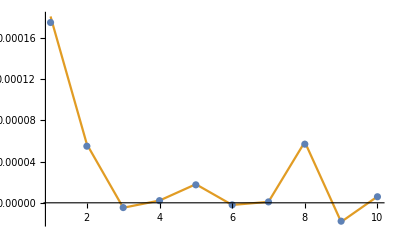

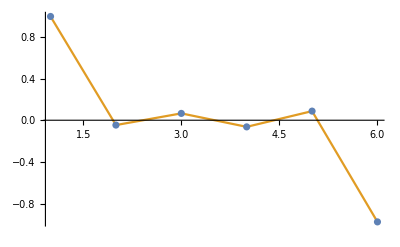

```mathematica
listedCovar1={covar[[1,1]],covar[[1,2]],covar[[1,3]],covar[[1,4]],covar[[2,2]],covar[[2,3]],covar[[2,4]],covar[[3,3]],covar[[3,4]],covar[[4,4]]};
listedCovar2={final4D[[1,1]],final4D[[1,2]],final4D[[1,3]],final4D[[1,4]],final4D[[2,2]],final4D[[2,3]],final4D[[2,4]],final4D[[3,3]],final4D[[3,4]],final4D[[4,4]]};
listedCorr1={corr[[1,2]],corr[[1,3]],corr[[1,4]],corr[[2,3]],corr[[2,4]],corr[[3,4]]};
listedCorr2={corr2[[1,2]],corr2[[1,3]],corr2[[1,4]],corr2[[2,3]],corr2[[2,4]],corr2[[3,4]]};

ListPlot[{listedCovar1,listedCovar2},Joined->{False, True}, PlotRange->All]
ListPlot[{listedCorr1,listedCorr2},Joined->{False, True}, PlotRange->All]
```

## Phase Shift Investigation (x)

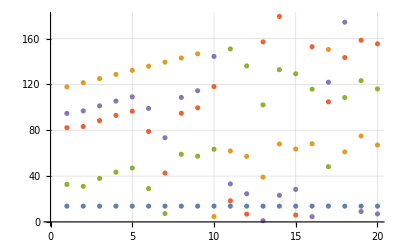

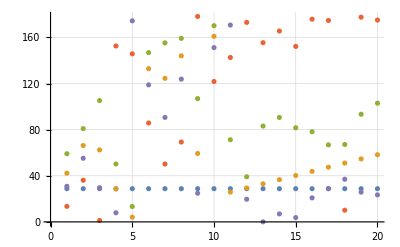

```mathematica
(*phaseShift0220=Transpose[comboEndTwiss,{1,3,2}][[1,6]]-comboStartTwiss[[1,6]];*)
comboEndTwiss2=Transpose[comboEndTwiss,{2,1,3}] ;
phaseShiftX=comboEndTwiss2[[;;,;;,3]]-comboStartTwiss[[1,3]];
phaseShiftY=comboEndTwiss2[[;;,;;,6]]-comboStartTwiss[[1,6]];
(*pointList=Transpose[{Range[Length@phaseShift0220],phaseShift0220}];*)
(*ListPlot[Drop[pointList,-3]]*)
ListPlot[
Mod[phaseShiftX*360,180]
,GridLines->Automatic]

ListPlot[
Mod[phaseShiftY*360,180]
,GridLines->Automatic]
```

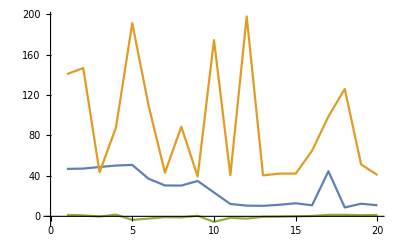

```mathematica
(*ListPlot[measurements02]*)
ListPlot[
Transpose[wsVars["20"]]
, PlotRange->All
,AxesOrigin->{0,0}
,Joined->True
]
```

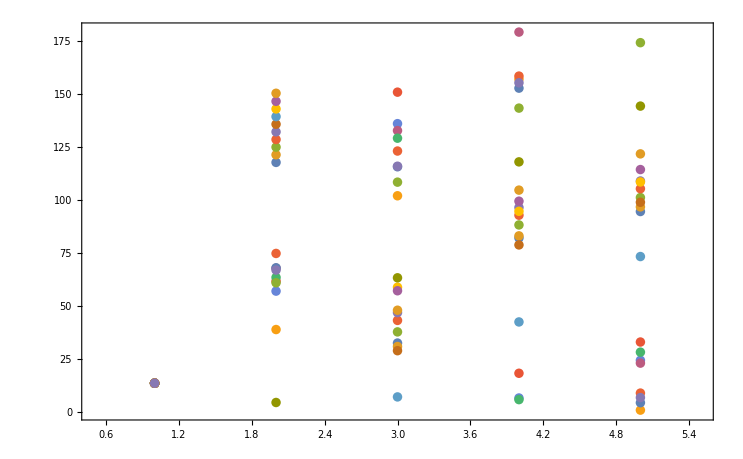

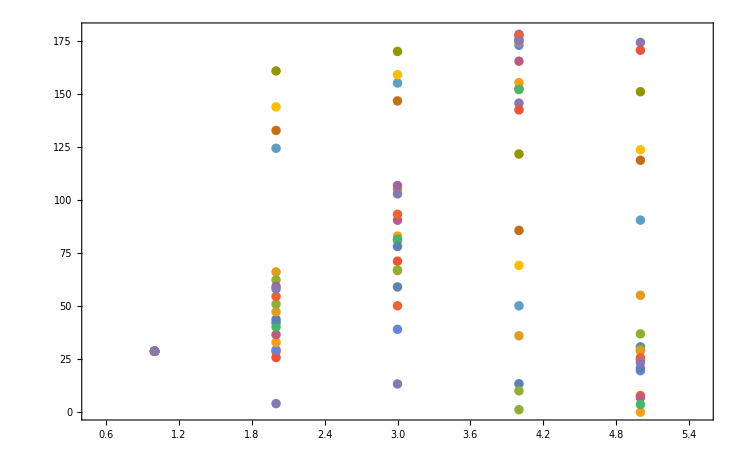

```mathematica
ListPlot[
Mod[Transpose@phaseShiftX*360,180],
PlotRange->{{.5,5.5},{0,180}},
Frame->True
]
ListPlot[
Mod[Transpose@phaseShiftY*360,180],
PlotRange->{{0.5,5.5},{0,180}},
Frame->True
]
```

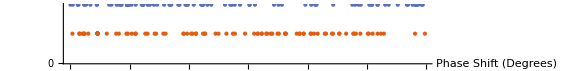

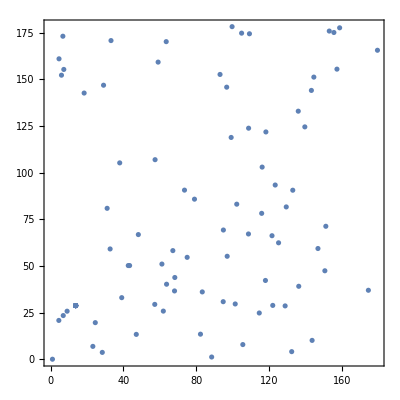

```mathematica
(*NumberLinePlot[Flatten[Mod[phaseShiftX*360,180]]]
NumberLinePlot[Flatten[Mod[phaseShiftY*360,180]]]
NumberLinePlot[Interval[{0,180}]]*)
NumberLinePlot[{Flatten[Mod[phaseShiftX*360,180]],Flatten[Mod[phaseShiftY*360,180]]},PlotTheme->"DarkColor",ImageSize-> Large,Ticks->{Range[0,180,30]},AxesLabel->{HoldForm["Phase Shift (Degrees)"],None}, PlotLegends->Placed[{"x","y"},Left]]

ListPlot[
Transpose@{
Flatten[Mod[phaseShiftX*360,180]],
Flatten[Mod[phaseShiftY*360,180]]
},
AspectRatio->1,
Frame->True
]
```

## Twiss Plotter

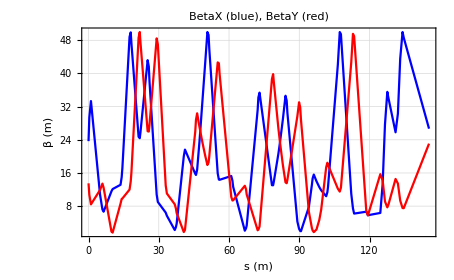

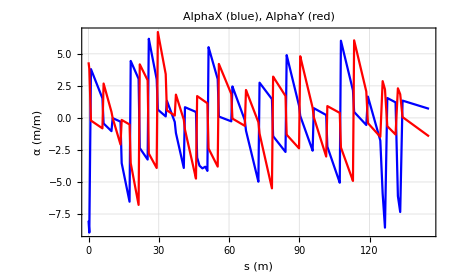

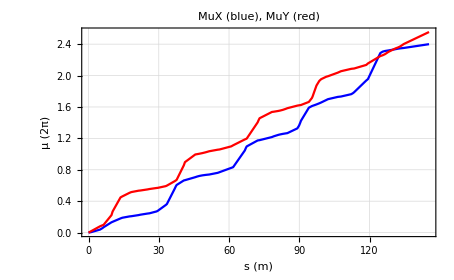

```mathematica
(* choose optics set *)
whichOptics=1;
elements=Normal[comboDataSets[[whichOptics]][[All,"NAME"]]];
twiss=getTwissAtElement[elements[[#]],comboDataSets[[whichOptics]]]&/@Range[Length@elements];

betaX=twiss[[#,1]] &/@ Range[Length@elements];
alphaX=twiss[[#,2]] &/@ Range[Length@elements];
muX=twiss[[#,3]] &/@ Range[Length@elements];
betaY=twiss[[#,4]] &/@ Range[Length@elements];
alphaY=twiss[[#,5]] &/@ Range[Length@elements];
muY=twiss[[#,6]] &/@ Range[Length@elements];
(* 1 through 6 for "BETX","ALFX","MUX","BETY","ALFY","MUY" *)

sVals=getSAtElement[elements[[#]],comboDataSets[[whichOptics]]]&/@Range[Length@elements];
Length@elements;

bx=ListPlot[
{Transpose[{sVals,betaX}]},
PlotStyle->Blue,
Joined->True,
GridLines->Automatic
];
by=ListPlot[
{Transpose[{sVals,betaY}]},
PlotStyle->Red,
Joined->True,
GridLines->Automatic
];
ax=ListPlot[
{Transpose[{sVals,alphaX}]},
PlotStyle->Blue,
Joined->True,
GridLines->Automatic
];
ay=ListPlot[
{Transpose[{sVals,alphaY}]},
PlotStyle->Red,
Joined->True,
GridLines->Automatic
];
mx=ListPlot[ (* left in units of 2pi *)
{Transpose[{sVals,muX}]},
PlotStyle->Blue,
Joined->True,
GridLines->Automatic
];
my=ListPlot[(* left in units of 2pi *)
{Transpose[{sVals,muY}]},
PlotStyle->Red,
Joined->True,
GridLines->Automatic
];
Show[bx,by,PlotRange->All,Frame->True,AxesLabel->None,FrameLabel->{{HoldForm[HoldForm["β (m)"]],None},{HoldForm[HoldForm["s (m)"]],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{"BetaX"," ",RowBox[{"(","blue",")"}]}],","," ",RowBox[{"BetaY"," ",RowBox[{"(","red",")"}]}]}]],LabelStyle->{FontFamily->"Titillium Web",13,GrayLevel[0]}]

Show[ax,ay,PlotRange->All,Frame->True,AxesLabel->None,FrameLabel->{{HoldForm[HoldForm["α (m/m)"]],None},{HoldForm[HoldForm["s (m)"]],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{"AlphaX"," ",RowBox[{"(","blue",")"}]}],","," ",RowBox[{"AlphaY"," ",RowBox[{"(","red",")"}]}]}]],LabelStyle->{FontFamily->"Titillium Web",13,GrayLevel[0]}]

Show[mx,my,PlotRange->All,Frame->True,AxesLabel->None,FrameLabel->{{HoldForm[HoldForm["μ (2π)"]],None},{HoldForm[HoldForm["s (m)"]],None}},PlotLabel->RawBoxes[RowBox[{RowBox[{"MuX"," ",RowBox[{"(","blue",")"}]}],","," ",RowBox[{"MuY"," ",RowBox[{"(","red",")"}]}]}]],LabelStyle->{FontFamily->"Titillium Web",13,GrayLevel[0]}]
```

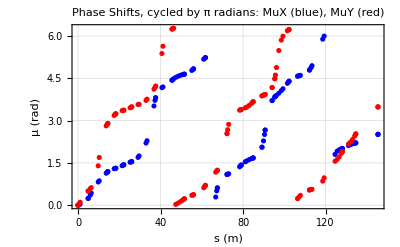

```mathematica
mx2=ListPlot[ (* left in units of 2pi *)
{Transpose[{sVals,Mod[muX*2π,2π]}]},
PlotStyle->Blue,
(*Joined->True,*)
GridLines->Automatic
];
my2=ListPlot[(* left in units of 2pi *)
{Transpose[{sVals,Mod[muY*2π,2π]}]},
PlotStyle->Red,
(*Joined->True,*)
GridLines->Automatic
];
Show[mx2,my2,PlotRange->All,Frame->True,AxesLabel->None,FrameLabel->{{HoldForm[HoldForm["μ (rad)"]],None},{HoldForm[HoldForm["s (m)"]],None}},PlotLabel->"Phase Shifts, cycled by π radians:  MuX (blue),  MuY (red)",LabelStyle->{FontFamily->"Titillium Web",12,GrayLevel[0]}]
```

## Discussion

### Tests:

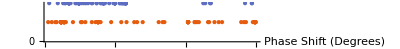

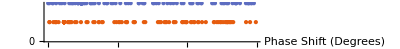

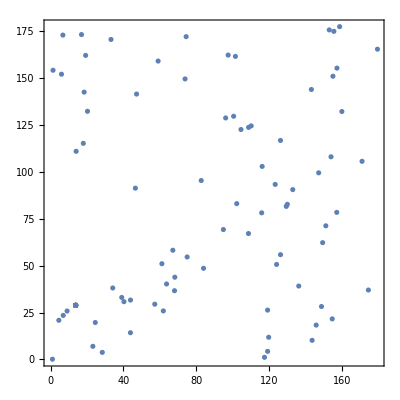

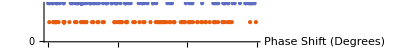

```mathematica
comboDataHeaders;
getSAtElement["WS24", comboDataSets[[1]]]
```

112.191